## Derivation of the governing equations

### Position of the fish in the global coordinate system (xf,yf)

```mathematica
rf={xf,yf};
```

### Unit vectors defining the swimming directions and its orthogonal vector, so that vperp = Cross[k, vuv]

```mathematica
kuv={0,0,1};
```

```mathematica
vuv={Cos[θ],Sin[θ]};
vuvn={Cos[θ],-Sin[θ]};
```

```mathematica
vperp=Delete[Cross[kuv,Join[vuv,{0}]],3];
```

### Velocity potential generated by the fish at the generic position r = (x,y)

```mathematica
r={x,y};
```

```mathematica
ϕf=-v r0^2 (Dot[(r-rf),vuv]/Norm[r-rf]^2);
```

### Advective velocity field generated by the fish at the generic point (x,y) (note the verification of Eq. (24) in the Appendix)

```mathematica
Ufcalc={FullSimplify[D[ϕf,x],{Element[x, Reals],Element[xf, Reals],Element[y, Reals],Element[yf, Reals]}],
FullSimplify[D[ϕf,y],{Element[x, Reals],Element[xf, Reals],Element[y, Reals],Element[yf, Reals]}]};
```

```mathematica
Uf={(r0^2 v ((x-xf+y-yf) (x-xf-y+yf) Cos[θ]+2 (x-xf) (y-yf) Sin[θ]))/(((xf-x)^2+(yf-y)^2)^2),(r0^2 v (2 (x-xf) (y-yf) Cos[θ]-(x-xf+y-yf) (x-xf-y+yf) Sin[θ]))/(((xf-x)^2+(yf-y)^2)^2)};
```

```mathematica
Uf-Ufcalc//FullSimplify
```

{0,0}

### Velocity potential generated by the interaction between the fish and the wall at the generic position r = (x,y) (note the verification of Eq. (25) in the Appendix for arbitrary parameter choice)

```mathematica
rdnp={xf,yf-2 (n+1) h};
rdnm={xf,-yf-2 n h};
runp={xf,yf+2 (n+1) h};
runm={xf,-yf+2 (n+1) h};
```

```mathematica
ρdnp=Simplify[Norm[r-rdnp],{Element[x,Reals],Element[xf,Reals],Element[y,Reals],Element[yf,Reals],Element[h,Reals],Element[n,Integers],h>0}];
ρdnm=Simplify[Norm[r-rdnm],{Element[x,Reals],Element[xf,Reals],Element[y,Reals],Element[yf,Reals],Element[h,Reals],Element[n,Integers],h>0}];
ρunp=Simplify[Norm[r-runp],{Element[x,Reals],Element[xf,Reals],Element[y,Reals],Element[yf,Reals],Element[h,Reals],Element[n,Integers],h>0}];
ρunm=Simplify[Norm[r-runm],{Element[x,Reals],Element[xf,Reals],Element[y,Reals],Element[yf,Reals],Element[h,Reals],Element[n,Integers],h>0}];
```

```mathematica
ϕid=-v r0^2 Sum[(Dot[(r-rdnp),vuv]/ρdnp^2)+(Dot[(r-rdnm),vuvn]/ρdnm^2),{n,0,∞}]//Simplify;
```

```mathematica
ϕiu=-v r0^2 Sum[(Dot[(r-runp),vuv]/ρunp^2)+(Dot[(r-runm),vuvn]/ρunm^2),{n,0,∞}]//Simplify;
```

```mathematica
ϕi=ϕid+ϕiu;;
```

```mathematica
ϕirev=1/4 r0^2 v (1/h E^(-I θ) (-E^(2 I θ) π (Coth[(π (x-xf+I (y-yf)))/(2h)]+Coth[(π (x-xf-I (y+yf)))/(2h)])-π (Coth[(π (x-xf-I y+I yf))/(2h)]+Coth[(π (x-xf+I (y+yf)))/(2h)]))+(4 (x-xf) Cos[θ]+4 (y-yf) Sin[θ])/((x-xf)^2+(y-yf)^2));
```

```mathematica
ϕirev-ϕi/.{r0->1, v->3,h->10,x->0.3,xf->0.5,y->2,yf->4,θ->0.6}//FullSimplify
```

-5.55112×10^-17+8.32667×10^-17 ⅈ

### Advective velocity fields generated by the interaction between the fish and the wall at the generic point (x,y) and at the very location of the fish (note that the walls are placed at 0 and h)

```mathematica
UwallGEN={D[ϕirev,x],D[ϕirev,y]};
```

```mathematica
Uw=Limit[Limit[UwallGEN,y->yf],x->xf]
```

{-(ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)) π^2 r0^2 v (1+3 Csc[(π yf)/h]^2))/(24 h^2),(ⅈ ⅇ^(-ⅈ θ) (-1+ⅇ^(2 ⅈ θ)) π^2 r0^2 v (-1+3 Csc[(π yf)/h]^2))/(24 h^2)}

### Velocity along the walls, confirming they are streamlines (vertical velocity component should be zero) and streamlines in the channel, with illustration for a parameter choice

```mathematica
FullSimplify[Limit[(Uf+UwallGEN),y->0],h>0]
```

{(ⅇ^(-ⅈ θ) π^2 r0^2 v (ⅇ^(2 ⅈ θ) Csch[(π (x-xf-ⅈ yf))/(2 h)]^2+Csch[(π (x-xf+ⅈ yf))/(2 h)]^2))/(4 h^2),0}

```mathematica
FullSimplify[Limit[(Uf+UwallGEN),y->h],h>0]
```

{(ⅇ^(-ⅈ θ) π^2 r0^2 v (Csch[(π (-ⅈ h+x-xf+ⅈ yf))/(2 h)]^2+ⅇ^(2 ⅈ θ) (Csch[(π (x-xf+ⅈ (h-yf)))/(2 h)]^2+Csch[(π (x-xf-ⅈ (h+yf)))/(2 h)]^2)+Csch[(π (x-xf+ⅈ (h+yf)))/(2 h)]^2))/(8 h^2),0}

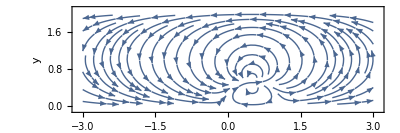

```mathematica
StreamPlot[(Uf+UwallGEN)/.{r0->1,v->3,h->2,θ->0,xf->0.5,yf->0.5},{x,-3,3},{y,0,2},AspectRatio->1/3,FrameLabel->{"x","y"}]
```

### Advective velocity fields from the background flow and streamlines in the channel, with illustration for a parameter choice

```mathematica
Ub=U0({1,0}-4 ϵ {((y-h/2)/h)^2,0})
```

{U0 (1-(4 (-h/2+y)^2 ϵ)/h^2),0}

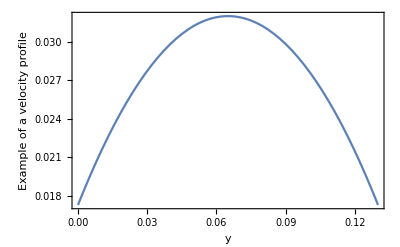

```mathematica
Plot[Ub[[1]]/.{U0->0.032,ϵ->.46,h->0.13},{y,0,.13},Frame->True,FrameLabel->{"y","Example of a velocity profile"}]
```

### Gradients of the velocity fields in the global coordinate system (U is Eq. (7) and UREV is used for the computation of Eq. (8))

```mathematica
U=Uw+Ub/.{x->xf,y->yf}
```

{U0 (1-(4 (-h/2+yf)^2 ϵ)/h^2)-(ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)) π^2 r0^2 v (1+3 Csc[(π yf)/h]^2))/(24 h^2),(ⅈ ⅇ^(-ⅈ θ) (-1+ⅇ^(2 ⅈ θ)) π^2 r0^2 v (-1+3 Csc[(π yf)/h]^2))/(24 h^2)}

```mathematica
UREV=UwallGEN+Ub;
GradUREV=Limit[Limit[{{D[UREV[[1]],x],D[UREV[[1]],y]},{D[UREV[[2]],x],D[UREV[[2]],y]}},y->yf],x->xf];
```

### Bias on the fish from the hydrodynamics under the assumption of T-dipole (Eq. (8))

```mathematica
Ω=-Dot[GradUREV. vperp,vuv]//FullSimplify
```

(Cos[θ] (-16 h U0 (h-2 yf) ϵ Cos[θ]-π^3 r0^2 v Cot[(π yf)/h] Csc[(π yf)/h]^2))/(4 h^3)

### Alternative bias on the fish from the hydrodynamics under the assumption of A-dipole (Eq. (30) in the Appendix)

```mathematica
ΩA=Dot[GradUREV. vuv,vperp]//FullSimplify
```

(π^3 r0^2 v Cos[θ] Cot[(π yf)/h] Csc[(π yf)/h]^2-16 h U0 (h-2 yf) ϵ Sin[θ]^2)/(4 h^3)

### Feedback system based on local circulation, with only the bottom half capable of sensing (note that the K here incorporates r0 and l with respect to Eq. (9))

```mathematica
vort[y_]=- D[Ub[[1]],y]
```

(8 U0 (-h/2+y) ϵ)/h^2

```mathematica
Ω1feedback=K vort[y]/.{y->yf,x->xf}//FullSimplify
```

-(4 K U0 (h-2 yf) ϵ)/h^2

## Analysis of governing equations

### 3D equations for xf, yf, and θ

```mathematica
(v vuv+U)//Simplify
```

{U0 (1-((h-2 yf)^2 ϵ)/h^2)+v Cos[θ]-(ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)) π^2 r0^2 v (1+3 Csc[(π yf)/h]^2))/(24 h^2),(ⅈ ⅇ^(-ⅈ θ) (-1+ⅇ^(2 ⅈ θ)) π^2 r0^2 v (-1+3 Csc[(π yf)/h]^2))/(24 h^2)+v Sin[θ]}

```mathematica
(Ω+Ω1feedback)//Simplify
```

-(16 h K U0 (h-2 yf) ϵ+16 h U0 (h-2 yf) ϵ Cos[θ]^2+π^3 r0^2 v Cos[θ] Cot[(π yf)/h] Csc[(π yf)/h]^2)/(4 h^3)

```mathematica
f3D[xf_,yf_,θ_]=Join[(v vuv+U),{(Ω+Ω1feedback)}]//Simplify
```

{U0 (1-((h-2 yf)^2 ϵ)/h^2)+v Cos[θ]-(ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)) π^2 r0^2 v (1+3 Csc[(π yf)/h]^2))/(24 h^2),(ⅈ ⅇ^(-ⅈ θ) (-1+ⅇ^(2 ⅈ θ)) π^2 r0^2 v (-1+3 Csc[(π yf)/h]^2))/(24 h^2)+v Sin[θ],-(16 h K U0 (h-2 yf) ϵ+16 h U0 (h-2 yf) ϵ Cos[θ]^2+π^3 r0^2 v Cos[θ] Cot[(π yf)/h] Csc[(π yf)/h]^2)/(4 h^3)}

```mathematica
D[f3D[xf,yf,θ],xf]
```

{0,0,0}

```mathematica
D[f3D[xf,yf,θ],yf]//Simplify
```

{(16 h U0 (h-2 yf) ϵ+ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)) π^3 r0^2 v Cot[(π yf)/h] Csc[(π yf)/h]^2)/(4 h^3),-(ⅈ ⅇ^(-ⅈ θ) (-1+ⅇ^(2 ⅈ θ)) π^3 r0^2 v Cot[(π yf)/h] Csc[(π yf)/h]^2)/(4 h^3),(8 K U0 ϵ)/h^2+(8 U0 ϵ Cos[θ]^2)/h^2+(π^4 r0^2 v (2+Cos[(2 π yf)/h]) Cos[θ] Csc[(π yf)/h]^4)/(4 h^4)}

```mathematica
D[f3D[xf,yf,θ],θ]//Simplify
```

{(ⅈ ⅇ^(-ⅈ θ) (-1+ⅇ^(2 ⅈ θ)) v (12 h^2-7 π^2 r0^2+(-12 h^2+π^2 r0^2) Cos[(2 π yf)/h]) Csc[(π yf)/h]^2)/(48 h^2),-(ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)) v (-12 h^2+5 π^2 r0^2+(12 h^2+π^2 r0^2) Cos[(2 π yf)/h]) Csc[(π yf)/h]^2)/(48 h^2),((32 h U0 (h-2 yf) ϵ Cos[θ]+π^3 r0^2 v Cot[(π yf)/h] Csc[(π yf)/h]^2) Sin[θ])/(4 h^3)}

### Simplification to 2 D, since axial coordinate is given by other two variables (α=ϵ U0/v, ρ2=r0^2/h^2, η=y/h, tND=h/v, bl=BL/h)

```mathematica
f2D[yf_,θ_]={f3D[xf,yf,θ][[2]],f3D[xf,yf,θ][[3]]}
```

{(ⅈ ⅇ^(-ⅈ θ) (-1+ⅇ^(2 ⅈ θ)) π^2 r0^2 v (-1+3 Csc[(π yf)/h]^2))/(24 h^2)+v Sin[θ],-(16 h K U0 (h-2 yf) ϵ+16 h U0 (h-2 yf) ϵ Cos[θ]^2+π^3 r0^2 v Cos[θ] Cot[(π yf)/h] Csc[(π yf)/h]^2)/(4 h^3)}

```mathematica
f2DND[η_,θ_]={Sin[θ](1-π^2/12 ρ2 (-1+3 Csc[π η]^2)),-4 α (1-2η)(K+Cos[θ]^2)-π^3/4 ρ2 Cos[θ]Cot[π η] Csc[π η]^2}
```

{(1-1/12 π^2 ρ2 (-1+3 Csc[π η]^2)) Sin[θ],-4 α (1-2 η) (K+Cos[θ]^2)-1/4 π^3 ρ2 Cos[θ] Cot[π η] Csc[π η]^2}

```mathematica
(f2DND[η,θ]-{f2D[η h,θ][[1]]/(v),f2D[η h,θ][[2]]/(v/h)})/.{ρ2->r0^2/h^2,α->U0 ϵ/v,bl->BL/h}//Simplify
```

{0,0}

### 2D equation centered around zero, so that we shift η up of 1/2 (the new coordinate is called ξ as in the paper; note that we verify Eq. (10)). We also plot some of the key functions to support the claims in the text

```mathematica
f2DNDcent[ξ_,θ_]={Sin[θ](1-π^2/12 ρ2 (-1+3 Csc[π (ξ+1/2)]^2)),4 α (2ξ)(K+Cos[θ]^2)-π^3/4 ρ2 Cos[θ]Cot[π (ξ+1/2)] Csc[π (ξ+1/2)]^2}
```

{(1-1/12 π^2 ρ2 (-1+3 Csc[π (1/2+ξ)]^2)) Sin[θ],8 α ξ (K+Cos[θ]^2)-1/4 π^3 ρ2 Cos[θ] Cot[π (1/2+ξ)] Csc[π (1/2+ξ)]^2}

```mathematica
f2DNDcent[ξ,θ]-f2DND[ξ+1/2,θ]//Simplify
```

{0,0}

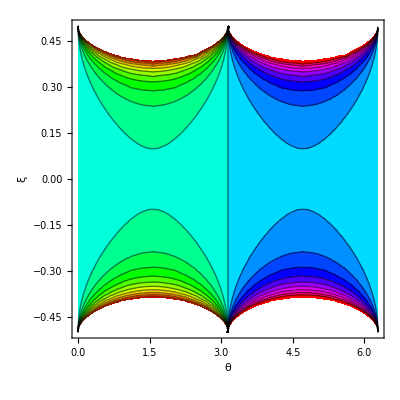

```mathematica
ContourPlot[(-Sin[θ] π^2/12 (-1+3 Csc[π (ξ+1/2)]^2)),{θ,0,2π},{ξ,-1/2,1/2},FrameLabel->{"θ","ξ","effect of wall on ydot"},Contours->20,ColorFunction->Hue]
```

```mathematica
Cot[π (1/2+ξ)] Csc[π (1/2+ξ)]^2/.ξ->1/4
```

-2

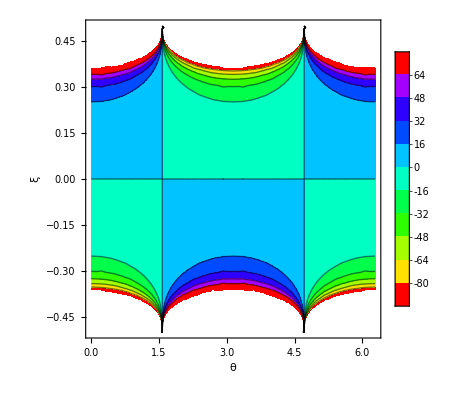

```mathematica
ContourPlot[(-1/4 π^3  Cos[θ] Cot[π (1/2+ξ)] Csc[π (1/2+ξ)]^2),{θ,0,2π},{ξ,-1/2,1/2},FrameLabel->{"θ","ξ","effect of wall on θdot"},Contours->10,PlotLegends->Automatic,ColorFunction->Hue]
```

### 2D equation centered around zero for the case of A-dipole (Eq. (31) in the Appendix)

```mathematica
f3DA[xf_,yf_,θ_]=Join[(v vuv+U),{(ΩA+Ω1feedback)}]//Simplify
```

{U0 (1-((h-2 yf)^2 ϵ)/h^2)+v Cos[θ]-(ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)) π^2 r0^2 v (1+3 Csc[(π yf)/h]^2))/(24 h^2),(ⅈ ⅇ^(-ⅈ θ) (-1+ⅇ^(2 ⅈ θ)) π^2 r0^2 v (-1+3 Csc[(π yf)/h]^2))/(24 h^2)+v Sin[θ],(8 h U0 (h-2 yf) ϵ (-1-2 K+Cos[2 θ])+π^3 r0^2 v Cos[θ] Cot[(π yf)/h] Csc[(π yf)/h]^2)/(4 h^3)}

```mathematica
f2DA[yf_,θ_]={f3DA[xf,yf,θ][[2]],f3DA[xf,yf,θ][[3]]}
```

{(ⅈ ⅇ^(-ⅈ θ) (-1+ⅇ^(2 ⅈ θ)) π^2 r0^2 v (-1+3 Csc[(π yf)/h]^2))/(24 h^2)+v Sin[θ],(8 h U0 (h-2 yf) ϵ (-1-2 K+Cos[2 θ])+π^3 r0^2 v Cos[θ] Cot[(π yf)/h] Csc[(π yf)/h]^2)/(4 h^3)}

```mathematica
f2DNDA[η_,θ_]={Sin[θ](1-π^2/12 ρ2 (-1+3 Csc[π η]^2)),-4 α (1-2η)(K+Sin[θ]^2)+π^3/4 ρ2 Cos[θ]Cot[π η] Csc[π η]^2}
```

{(1-1/12 π^2 ρ2 (-1+3 Csc[π η]^2)) Sin[θ],1/4 π^3 ρ2 Cos[θ] Cot[π η] Csc[π η]^2-4 α (1-2 η) (K+Sin[θ]^2)}

```mathematica
(f2DNDA[η,θ]-{f2DA[η h,θ][[1]]/(v),f2DA[η h,θ][[2]]/(v/h)})/.{ρ2->r0^2/h^2,α->U0 ϵ/v,bl->BL/h}//Simplify
```

{0,0}

```mathematica
f2DNDcentA[ξ_,θ_]={Sin[θ](1-π^2/12 ρ2 (-1+3 Csc[π (ξ+1/2)]^2)),4 α (2ξ)(K+Sin[θ]^2)+π^3/4 ρ2 Cos[θ]Cot[π (ξ+1/2)] Csc[π (ξ+1/2)]^2}
```

{(1-1/12 π^2 ρ2 (-1+3 Csc[π (1/2+ξ)]^2)) Sin[θ],1/4 π^3 ρ2 Cos[θ] Cot[π (1/2+ξ)] Csc[π (1/2+ξ)]^2+8 α ξ (K+Sin[θ]^2)}

```mathematica
f2DNDcentA[ξ,θ]-f2DNDA[ξ+1/2,θ]//Simplify
```

{0,0}

## Detailed analysis of the 2D equations

### Nullclines (dξ/dt=Sin[θ]gξ[ξ], dθ/dt=gθ[ξ,θ])

```mathematica
f2DNDcent[ξ,θ]
```

{(1-1/12 π^2 ρ2 (-1+3 Csc[π (1/2+ξ)]^2)) Sin[θ],8 α ξ (K+Cos[θ]^2)-1/4 π^3 ρ2 Cos[θ] Cot[π (1/2+ξ)] Csc[π (1/2+ξ)]^2}

```mathematica
gξ[ξ_]=(1-1/12 π^2 ρ2 (-1+3 Csc[π (1/2+ξ)]^2));
```

```mathematica
gθ[ξ_,θ_]=8 α ξ (K+Cos[θ]^2)-1/4 π^3 ρ2 Cos[θ] Cot[π (1/2+ξ)] Csc[π (1/2+ξ)]^2;
```

```mathematica
f2DNDcent[ξ,θ]-{gξ[ξ]Sin[θ],gθ[ξ,θ]}//Simplify
```

{0,0}

#### For θ = π, we have two potential positions if we swim upstream (equation on dξ/dt=0 is automatically satisfied) provided that ρtilde=ρ2/(α(1+K))<32/π^4 and ξ=0; for θ = 0, we have only θ=0. Plots below are presented as Fig. 4

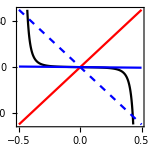

```mathematica
auxgen[ξ_]=1/32 π^3  Cot[π (1/2+ξ)] Csc[π (1/2+ξ)]^2;
Fungen=Plot[{auxgen[ξ],200ξ,-200ξ,-2ξ},{ξ,-1/2,1/2},PlotStyle->{Black,Red,{Blue,Dashed},Blue},PlotRange->{{-0.5,0.5},{-100,100}},Frame->True,FrameLabel->{"ξ"},ImageSize->150,AspectRatio->1]
```

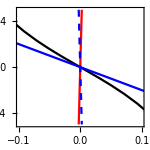

```mathematica
Fungenzoom=Plot[{auxgen[ξ],200ξ,-200ξ,-2ξ},{ξ,-0.5,0.5},PlotStyle->{Black,Red,{Blue,Dashed},Blue},PlotRange->{{-0.1,0.1},{-0.5,0.5}},Frame->True,FrameLabel->{"ξ"},ImageSize->150,AspectRatio->1]
```

```mathematica
auxgen'[0]
```

-π^4/32

Computations of Landau orders for supporting the inequalities in the paper for ρ small (text around Eqs. (21) and (22))

```mathematica
Limit[auxgen[ξ](ξ-1/2)^3,ξ->1/2]
```

1/32

```mathematica
Series[auxgen[ξ](ξ-1/2)^3,{ξ,1/2,4}]
```

1/32-1/480 π^4 (ξ-1/2)^4+O[ξ-1/2]^5

```mathematica
Limit[(1/Cos[π ξ]^2)(ξ-1/2)^2,ξ->1/2]
```

1/π^2

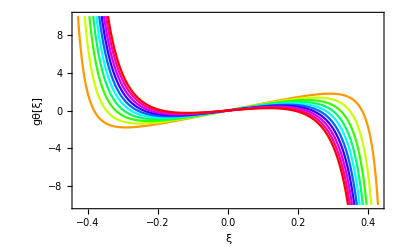

```mathematica
auxπ[ξ_]=8 ξ+1/4 π^3 ρtilde Cot[π (1/2+ξ)] Csc[π (1/2+ξ)]^2;
Plot[Table[auxπ[ξ]/.ρtilde->.02 i,{i,1,10}]//Evaluate,{ξ,-1/2,1/2},PlotStyle->Table[Hue[.1i],{i,1,10}],PlotRange->{All,{-10,10}},Frame->True,FrameLabel->{"ξ","gθ[ξ]","Swimming upstream"}]
```

```mathematica
auxπ'[0]
```

8-(π^4 ρtilde)/4

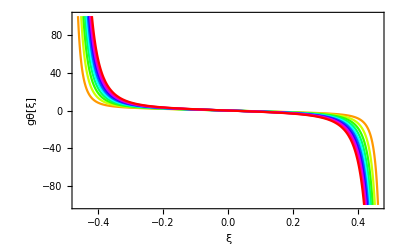

```mathematica
aux0[ξ_]=-8 ξ+1/4 π^3 ρtilde Cot[π (1/2+ξ)] Csc[π (1/2+ξ)]^2;
Plot[Table[aux0[ξ]/.ρtilde->.02 i,{i,1,10}]//Evaluate,{ξ,-1/2,1/2},PlotStyle->Table[Hue[.1i],{i,1,10}],PlotRange->{All,{-100,100}},Frame->True,FrameLabel->{"ξ","gθ[ξ]","Swimming downstream"}]
```

```mathematica
aux0'[0]
```

-8-(π^4 ρtilde)/4

### Perturbations to compute the linearized dynamics (Eq. (15))

```mathematica
Series[f2DNDcent[ξ,θ],{ξ,ξ0,1},{θ,θ0,1}]//Simplify
```

{(1/12 (12+π^2 ρ2-3 π^2 ρ2 Sec[π ξ0]^2) Sin[θ0]+1/12 Cos[θ0] (12+π^2 ρ2-3 π^2 ρ2 Sec[π ξ0]^2) (θ-θ0)+O[θ-θ0]^2)+(-1/2 π^3 ρ2 Sec[π ξ0]^2 Sin[θ0] Tan[π ξ0]-1/2 (π^3 ρ2 Cos[θ0] Sec[π ξ0]^2 Tan[π ξ0]) (θ-θ0)+O[θ-θ0]^2) (ξ-ξ0)+O[ξ-ξ0]^2,((8 K α ξ0+8 α ξ0 Cos[θ0]^2+1/4 π^3 ρ2 Cos[θ0] Sec[π ξ0]^2 Tan[π ξ0])-1/4 (Sin[θ0] (64 α ξ0 Cos[θ0]+π^3 ρ2 Sec[π ξ0]^2 Tan[π ξ0])) (θ-θ0)+O[θ-θ0]^2)+((8 K α+8 α Cos[θ0]^2-1/4 π^4 ρ2 Cos[θ0] (-2+Cos[2 π ξ0]) Sec[π ξ0]^4)+1/4 (-64 α Cos[θ0]+π^4 ρ2 (-2+Cos[2 π ξ0]) Sec[π ξ0]^4) Sin[θ0] (θ-θ0)+O[θ-θ0]^2) (ξ-ξ0)+O[ξ-ξ0]^2}

```mathematica
ANDgeneral[ξ0_,θ0_]={{-1/2 π^3 ρ2 Sec[π ξ0]^2 Sin[θ0] Tan[π ξ0],1/12 Cos[θ0] (12+π^2 ρ2-3 π^2 ρ2 Sec[π ξ0]^2)},{(8 K α+8 α Cos[θ0]^2-1/4 π^4 ρ2 Cos[θ0] (-2+Cos[2 π ξ0]) Sec[π ξ0]^4),(-8 α ξ0 Sin[2 θ0]-1/4 π^3 ρ2 Sec[π ξ0]^2 Sin[θ0] Tan[π ξ0])}}
```

{{-1/2 π^3 ρ2 Sec[π ξ0]^2 Sin[θ0] Tan[π ξ0],1/12 Cos[θ0] (12+π^2 ρ2-3 π^2 ρ2 Sec[π ξ0]^2)},{8 K α+8 α Cos[θ0]^2-1/4 π^4 ρ2 Cos[θ0] (-2+Cos[2 π ξ0]) Sec[π ξ0]^4,-8 α ξ0 Sin[2 θ0]-1/4 π^3 ρ2 Sec[π ξ0]^2 Sin[θ0] Tan[π ξ0]}}

### Linear stability analysis (Eqs. (16)-(22))

```mathematica
ANDgeneral[0,0]//Simplify
```

{{0,1-(π^2 ρ2)/6},{8 (1+K) α+(π^4 ρ2)/4,0}}

```mathematica
ANDgeneral[0,π]//Simplify
```

{{0,-1+(π^2 ρ2)/6},{8 (1+K) α-(π^4 ρ2)/4,0}}

```mathematica
Det[ANDgeneral[0,π]]//Simplify
```

1/24 (-6+π^2 ρ2) (-32 (1+K) α+π^4 ρ2)

```mathematica
ANDgeneral[ξ,π]//FullSimplify
```

{{0,-1-(π^2 ρ2)/12+1/4 π^2 ρ2 Sec[π ξ]^2},{8 (1+K) α+1/4 π^4 ρ2 (-2+Cos[2 π ξ]) Sec[π ξ]^4,0}}

```mathematica
Det[ANDgeneral[ξ,π]]//FullSimplify
```

-1/48 (-12-π^2 ρ2+3 π^2 ρ2 Sec[π ξ]^2) (32 (1+K) α+π^4 ρ2 (-2+Cos[2 π ξ]) Sec[π ξ]^4)

### Linear stability analysis for the A-dipole (Eqs. (33)-(39) in the Appendix)

```mathematica
Series[f2DNDcentA[ξ,θ],{ξ,ξ0,1},{θ,θ0,1}]//Simplify
```

{(1/12 (12+π^2 ρ2-3 π^2 ρ2 Sec[π ξ0]^2) Sin[θ0]+1/12 Cos[θ0] (12+π^2 ρ2-3 π^2 ρ2 Sec[π ξ0]^2) (θ-θ0)+O[θ-θ0]^2)+(-1/2 π^3 ρ2 Sec[π ξ0]^2 Sin[θ0] Tan[π ξ0]-1/2 (π^3 ρ2 Cos[θ0] Sec[π ξ0]^2 Tan[π ξ0]) (θ-θ0)+O[θ-θ0]^2) (ξ-ξ0)+O[ξ-ξ0]^2,((8 K α ξ0+8 α ξ0 Sin[θ0]^2-1/4 π^3 ρ2 Cos[θ0] Sec[π ξ0]^2 Tan[π ξ0])+1/4 Sin[θ0] (64 α ξ0 Cos[θ0]+π^3 ρ2 Sec[π ξ0]^2 Tan[π ξ0]) (θ-θ0)+O[θ-θ0]^2)+((1/4 π^4 ρ2 Cos[θ0] (-2+Cos[2 π ξ0]) Sec[π ξ0]^4+8 α (K+Sin[θ0]^2))+1/4 (64 α Cos[θ0]-π^4 ρ2 (-2+Cos[2 π ξ0]) Sec[π ξ0]^4) Sin[θ0] (θ-θ0)+O[θ-θ0]^2) (ξ-ξ0)+O[ξ-ξ0]^2}

```mathematica
ANDgeneralA[ξ0_,θ0_]={{-1/2 π^3 ρ2 Sec[π ξ0]^2 Sin[θ0] Tan[π ξ0],1/12 Cos[θ0] (12+π^2 ρ2-3 π^2 ρ2 Sec[π ξ0]^2)  },{1/4 π^4 ρ2 Cos[θ0] (-2+Cos[2 π ξ0]) Sec[π ξ0]^4+8 α (K+Sin[θ0]^2),1/4 Sin[θ0] (64 α ξ0 Cos[θ0]+π^3 ρ2 Sec[π ξ0]^2 Tan[π ξ0])}}
```

{{-1/2 π^3 ρ2 Sec[π ξ0]^2 Sin[θ0] Tan[π ξ0],1/12 Cos[θ0] (12+π^2 ρ2-3 π^2 ρ2 Sec[π ξ0]^2)},{1/4 π^4 ρ2 Cos[θ0] (-2+Cos[2 π ξ0]) Sec[π ξ0]^4+8 α (K+Sin[θ0]^2),1/4 Sin[θ0] (64 α ξ0 Cos[θ0]+π^3 ρ2 Sec[π ξ0]^2 Tan[π ξ0])}}

```mathematica
ANDgeneralA[0,0]//Simplify
```

{{0,1-(π^2 ρ2)/6},{8 K α-(π^4 ρ2)/4,0}}

```mathematica
Det[ANDgeneralA[0,0]]//Simplify
```

-1/24 (-6+π^2 ρ2) (-32 K α+π^4 ρ2)

```mathematica
ANDgeneralA[ξ,0]//FullSimplify
```

{{0,1/12 (12+π^2 ρ2-3 π^2 ρ2 Sec[π ξ]^2)},{8 K α+1/4 π^4 ρ2 (-2+Cos[2 π ξ]) Sec[π ξ]^4,0}}

```mathematica
Det[ANDgeneralA[ξ,0]]//FullSimplify
```

-1/96 (12-5 π^2 ρ2+(12+π^2 ρ2) Cos[2 π ξ]) (12 K α-2 π^4 ρ2+(16 K α+π^4 ρ2) Cos[2 π ξ]+4 K α Cos[4 π ξ]) Sec[π ξ]^6

```mathematica
Det[ANDgeneralA[ξ,0]]-1/48(12-3 π^2 ρ2 Sec[π ξ]^2+π^2 ρ2)(-32 K α+π^4 ρ2(2-Cos[2 π ξ]) Sec[π ξ]^4)//FullSimplify
```

0

```mathematica
ANDgeneralA[0,π]//Simplify
```

{{0,-1+(π^2 ρ2)/6},{8 K α+(π^4 ρ2)/4,0}}

```mathematica
Det[ANDgeneralA[0,π]]//Simplify
```

-1/24 (-6+π^2 ρ2) (32 K α+π^4 ρ2)

### Stability of rheotactic response close to the walls or at the center as a function of ρtilde (or its inverse beta as in Fig. 3) and demonstration of the inequality in Eq. (22)

```mathematica
Ntab=500;
ρtildenumtab=Table[i(32/π^4)/(Ntab+1),{i,1,Ntab}]//N;
ξ0tabWρ={};
For[i=1,i<Length[ρtildenumtab]+1,i++,
auxξKρ=ξ/.FindRoot[auxπ[ξ]/.ρtilde->ρtildenumtab[[i]],{ξ,0.49}];
AppendTo[ξ0tabWρ,auxξKρ];
]
```

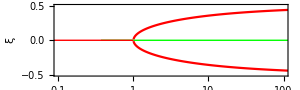

```mathematica
Bif=Show[ListLogLinearPlot[Table[{(ρtildenumtab[[i]]/(32/π^4))^(-1),ξ0tabWρ[[i]]},{i,1,Length[ρtildenumtab]}],PlotRange->{{0.1,100},{-.5,0.5}},Joined->True,Frame->True,FrameLabel->{"β/β^*","ξ"},PlotStyle->Red,AspectRatio->0.3,ImageSize->300,Axes->None],ListLogLinearPlot[Table[{(ρtildenumtab[[i]]/(32/π^4))^(-1),-ξ0tabWρ[[i]]},{i,1,Length[ρtildenumtab]}],Joined->True,PlotStyle->Red],Graphics[{Green,Thick,Line[{{-1,0},{0,0}}]}],Graphics[{Green,Thick,Line[{{0,0},{100,0}}]}],Graphics[{Red,Thick,Line[{{-10,0},{0,0}}]}]]
```

```mathematica
ff0[β_,ξ0_]=π^4  (2-Cos[2 π ξ0]) Sec[π ξ0]^4/32;
```

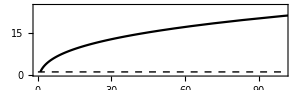

```mathematica
f0=Show[ListPlot[Table[{(ρtildenumtab[[i]]/(32/π^4))^(-1),ff0[(ρtildenumtab[[i]])^(-1),ξ0tabWρ[[i]]]/((ρtildenumtab[[i]])^(-1))},{i,1,Length[ρtildenumtab]}],Joined->True,PlotStyle->Black,PlotRange->{{0,100},{0,25}},Frame->True,FrameLabel->{"β/β^*",""},PlotStyle->Green,AspectRatio->0.3,ImageSize->300,Axes->None],Graphics[{Dashed,Line[{{0,1},{100,1}}]}]]
```

### Numerics

#### Nondimensional parameters

```mathematica
αnum=0.1
ρ2num=0.01
Knum=1;
```

0.1

0.01

```mathematica
Sqrt[ρ2num]
```

0.1

```mathematica
αnum/ρ2num
```

10.

```mathematica
(π^4)/32//N
```

3.04403

```mathematica
ρtildenum=ρ2num/(αnum(1+Knum));
1/ρtildenum
ρtildenum<32/π^4 //N
```

20.

True

#### Phase plots in Fig. 3

```mathematica
auxξ=ξ/.FindRoot[auxπ[ξ]/.ρtilde->ρ2num/(αnum(1+Knum)),{ξ,0.3}]
```

0.332874

```mathematica
auxA=ANDgeneral[ξ0,π]/.{α->αnum,ρ2->ρ2num,K->Knum,ξ0->auxξ}
```

{{0,-0.910019},{-8.03463,0}}

```mathematica
Eigenvalues[auxA]
```

{-2.70401,2.70401}

```mathematica
Eigenvalues[ANDgeneral[0,0]/.{α->αnum,ρ2->ρ2num,K->Knum,ξ0->auxξ}]
```

{-1.34655,1.34655}

```mathematica
Eigenvalues[ANDgeneral[0,π]/.{α->αnum,ρ2->ρ2num,K->Knum,ξ0->auxξ}]
```

{0.+1.15506 ⅈ,0.-1.15506 ⅈ}

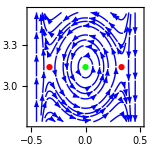

```mathematica
FigPhaseplot=Show[StreamPlot[{f2DNDcent[ξ,θ][[1]],f2DNDcent[ξ,θ][[2]]}/.{α->αnum,ρ2->ρ2num,K->Knum},{ξ,-1/2,1/2},{θ,π-0.4,π+0.4},StreamStyle->Blue,StreamScale->0.15,StreamPoints->Medium,FrameLabel->{"ξ","θ_f"},AspectRatio->1,ImageSize->150],Graphics[{PointSize[.03],Green,Point[{0,π}]}],Graphics[{PointSize[.03],Red,Point[{auxξ,π}]}],Graphics[{PointSize[.03],Red,Point[{-auxξ,π}]}]]
```

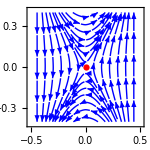

```mathematica
FigPhaseplot2=Show[StreamPlot[{f2DNDcent[ξ,θ][[1]],f2DNDcent[ξ,θ][[2]]}/.{α->αnum,ρ2->ρ2num,K->Knum},{ξ,-1/2,1/2},{θ,-0.4,+0.4},StreamStyle->Blue,StreamScale->0.15,StreamPoints->Medium,FrameLabel->{"ξ","θ_f"},AspectRatio->1,ImageSize->150],Graphics[{PointSize[.03],Red,Point[{0,0}]}]]
```

#### Phase plots equivalent to those in Fig. 3 but for an A-dipole (not included in the paper but useful to verify the stability claims)

```mathematica
auxξA=ξ/.FindRoot[auxπ[ξ]/.ρtilde->ρ2num/(αnum Knum),{ξ,0.3}]
```

0.277182

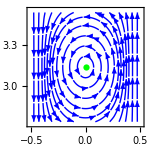

```mathematica
FigPhaseplotA=Show[StreamPlot[{f2DNDcentA[ξ,θ][[1]],f2DNDcentA[ξ,θ][[2]]}/.{α->αnum,ρ2->ρ2num,K->Knum},{ξ,-1/2,1/2},{θ,π-0.4,π+0.4},StreamStyle->Blue,StreamScale->0.15,StreamPoints->Medium,FrameLabel->{"ξ","θ_f"},AspectRatio->1,ImageSize->150],Graphics[{PointSize[.03],Green,Point[{0,π}]}]]
```

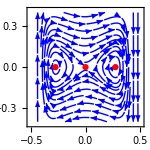

```mathematica
FigPhaseplot2A=Show[StreamPlot[{f2DNDcentA[ξ,θ][[1]],f2DNDcentA[ξ,θ][[2]]}/.{α->αnum,ρ2->ρ2num,K->Knum},{ξ,-1/2,1/2},{θ,-0.4,+0.4},StreamStyle->Blue,StreamScale->0.15,StreamPoints->Medium,FrameLabel->{"ξ","θ_f"},AspectRatio->1,ImageSize->150],Graphics[{PointSize[.03],Red,Point[{0,0}]}],Graphics[{PointSize[.03],Red,Point[{auxξA,0}]}],Graphics[{PointSize[.03],Red,Point[{-auxξA,0}]}]]
```

#### Simulation without noise

ICs close to rheotaxis

```mathematica
Ξ0=0.1;
Θ0=170 π/180//N
X0=0;
```

2.96706

Integration of the equations of motion for one example

```mathematica
tmax=50.;
ϵnum=0.3;
```

```mathematica
ODEs=Join[{Ξ'[t]==f2DNDcent[Ξ[t],Θ[t]][[1]]/.{α->αnum,ρ2->ρ2num,K->Knum}},{Θ'[t]==f2DNDcent[Ξ[t],Θ[t]][[2]]/.{α->αnum,ρ2->ρ2num,K->Knum}},{X'[t]==fNDcentx[Ξ[t],Θ[t]]/.{α->αnum,ρ2->ρ2num,K->Knum,ϵ->ϵnum}}];
```

```mathematica
ICs=Join[{Ξ[0]==Ξ0,Θ[0]==Θ0,X[0]==X0}];
```

```mathematica
sol=NDSolve[Evaluate[Join[ODEs,ICs]],{Ξ,Θ,X},{t,0.,tmax}];
```

```mathematica
{{Ξsol,Θsol,Xsol}}={Ξ,Θ,X}/.sol;
```

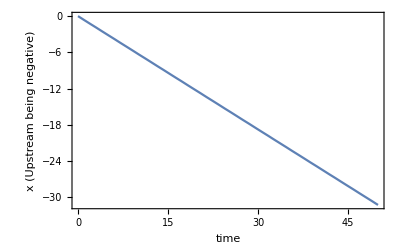

```mathematica
Plot[Xsol[t],{t,0,tmax},Frame->True,FrameLabel->{"time","x (Upstream being negative)"}]
```

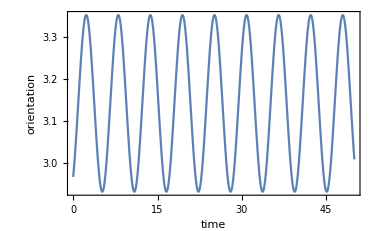

```mathematica
Plot[Θsol[t],{t,0,tmax},Frame->True,FrameLabel->{"time","orientation"}]
```

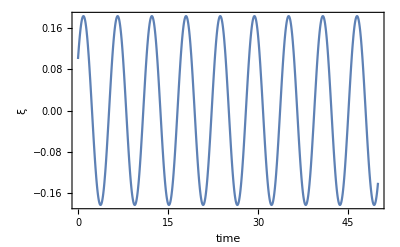

```mathematica
Plot[Ξsol[t],{t,0,tmax},Frame->True,FrameLabel->{"time","ξ"}]
```

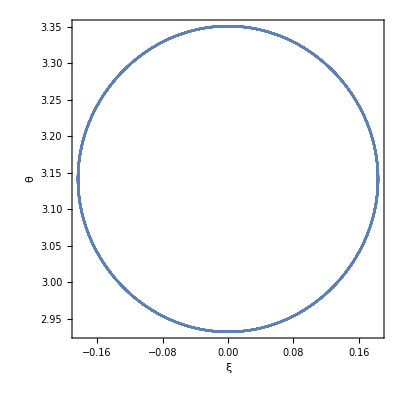

```mathematica
ParametricPlot[{Ξsol[t],Θsol[t]},{t,0.,tmax},PlotRange->All,AspectRatio->1,Frame->True,FrameLabel->{"ξ","θ"}]
```